```mathematica
Clear["Global*`"]
```

```mathematica
(*2*)
```

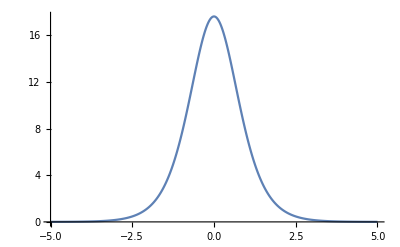

```mathematica
CalcWindow=5;(*ps*)
N0=2047;

N0=N0+Boole[EvenQ[N0]];
Sech2Imp[T0_]:=Table[(-β2/γ/T0^2)^(1/2)*N[Sech[t/T0]],{t,- CalcWindow, CalcWindow,2CalcWindow/(N0-1)}];

β2=-22;γ=1.25;
Imp=Fourier[Sech2Imp[1]];

D2Fourier=Table[-(Pi k/CalcWindow)^2,{k,0,N0/2}]~Join~Table[-(Pi (k-N0)/CalcWindow)^2,{k,Ceiling[N0/2],N0-1}];
FourierOp:=Exp[-I β2/2 D2Fourier h];
SpatialOp[x_List]:=Exp[I γ Abs[x]^2 h];

ListPlot[(Abs[InverseFourier[Imp]]^2),PlotRange->All,Joined->True,DataRange->{-CalcWindow, CalcWindow},AxesOrigin->{-CalcWindow,0}]
```

```mathematica
(*несимметричный SSFT*)
```

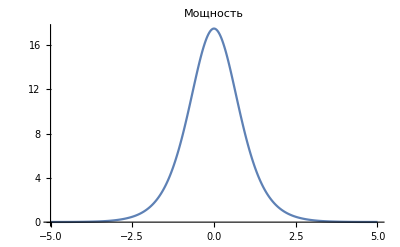

```mathematica
h=0.1/2048;
Imp=Fourier[Sech2Imp[1]];
For[ξ=h/2,ξ<1,ξ+=h,

Imp=FourierOp Imp;
Imp=InverseFourier[Imp];
Imp=Imp SpatialOp[Imp];
Imp=Fourier[Imp];

];
ImpEtSym=InverseFourier[Imp];
SymFit={};
h=0.05;
For[i=1,i<10,i+=1,
Imp=Fourier[Sech2Imp[1]];
Timing[Monitor[
For[ξ=h/2,ξ<1,ξ+=h,

Imp=FourierOp Imp;
Imp=InverseFourier[Imp];
Imp=Imp SpatialOp[Imp];
Imp=Fourier[Imp];

],ξ]][[1]];
Imp=InverseFourier[Imp];
AppendTo[SymFit,Log[2,Max[Abs[Imp-ImpEtSym]]]];
h=h/2;
];
ListPlot[(Abs[Imp]^2),PlotRange->All,Joined->True,DataRange->{-CalcWindow,CalcWindow},AxesOrigin->{-CalcWindow,0},PlotLabel->"Мощность"]
```

{a→1.37079,b→8.51422}

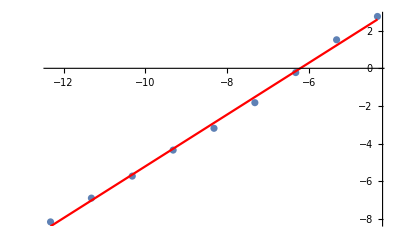

```mathematica
Clear[SFit]
SFit=Transpose[{Table[Log[2,0.1/2^i],{i,1,9}],SymFit}];
model=a x+b;
fitS=FindFit[SFit,model,{a,b},x]
Show[ListPlot[SFit],Plot[Evaluate[model /. fitS],{x,Min[SFit[[All,1]]],Max[SFit[[All,1]]]},PlotStyle->Red]]
```

```mathematica
(*симметричный SSFT*)
```

{28.2623,Null}

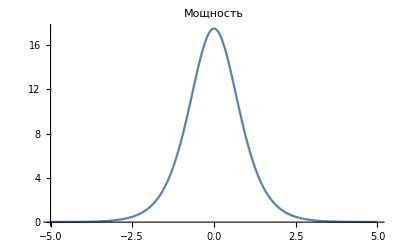

```mathematica
h=0.1/1024;
Imp=Fourier[Sech2Imp[1]];
Imp=Sqrt[FourierOp]Imp;
Timing[Monitor[
For[ξ=h/2,ξ<1,ξ+=h,

Imp=InverseFourier[Imp];
Imp=Imp SpatialOp[Imp];
Imp=Fourier[Imp];
Imp=FourierOp Imp

],ξ]]
Imp=InverseFourier[Imp/Sqrt[FourierOp]];
ImpEtNSym=Imp;
NSymFit={};
h=0.1;
For[i=1,i<10,i+=1,
Imp=Fourier[Sech2Imp[1]];
Imp=Sqrt[FourierOp]Imp;
Timing[Monitor[
For[ξ=h/2,ξ<1,ξ+=h,

Imp=InverseFourier[Imp];
Imp=Imp SpatialOp[Imp];
Imp=Fourier[Imp];
Imp=FourierOp Imp

],ξ]][[1]];
Imp=InverseFourier[Imp/Sqrt[FourierOp]];
AppendTo[NSymFit,Log[2,Max[Abs[Imp-ImpEtNSym]]]];
h=h/2;
];
ListPlot[(Abs[Imp]^2),PlotRange->All,Joined->True,DataRange->{-CalcWindow,CalcWindow},AxesOrigin->{-CalcWindow,0},PlotLabel->"Мощность"]
```

{a→1.82026,b→12.5683}

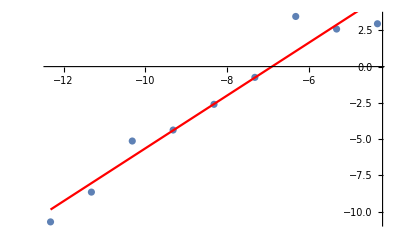

```mathematica
Clear[NSFit]
NSFit=Transpose[{Table[Log[2,0.1/2^i],{i,1,9}],NSymFit}];
model=a x+b;
fitNS=FindFit[NSFit,model,{a,b},x]
Show[ListPlot[NSFit],Plot[Evaluate[model /. fitNS],{x,Min[NSFit[[All,1]]],Max[NSFit[[All,1]]]},PlotStyle->Red]]
```

```mathematica
(*3*)
```

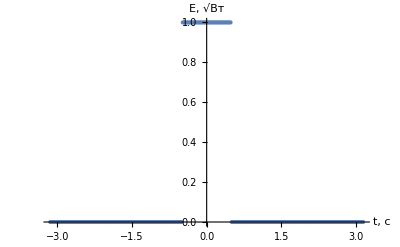

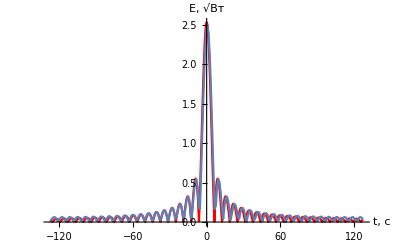

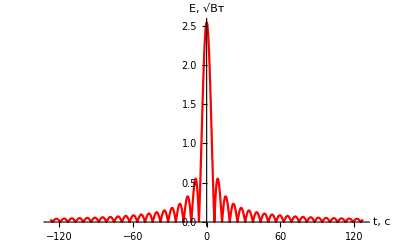

```mathematica
NN=255;
τ=1;
T=2*Pi;
fi[t_]:=HeavisidePi[t/τ];
(*fi[t_]:=Cos[5t];(*для aliasing: NN = 31 и 2047*)*)
fd=Table[fi[t],{t,-T/2,T/2,T/NN}];
ListPlot[fd,DataRange->{-T/2,T/2},AxesLabel->{"t, c","E, √(:0412:0442)"},LabelStyle->Directive[FontFamily->"Times New Roman",15]]
f[ω_]=FourierTransform[fi[t],t,ω];
fdf=RotateLeft[Fourier[fd],(NN+1)/2];
Show[Plot[Abs[f[ω]]/((T*√NN)/((NN-1)√(2*π))),{ω,-π*NN/T,π*NN/T},PlotStyle->Red,PlotRange->All,AxesLabel->{"t, c","E, √(:0412:0442)"},LabelStyle->Directive[FontFamily->"Times New Roman",15]],ListLinePlot[Abs[fdf],PlotRange->All,DataRange->{-π*NN/T,π*NN/T},AxesLabel->{"t, c","E, √(:0412:0442)"},LabelStyle->Directive[FontFamily->"Times New Roman",15]]]
Plot[Abs[f[ω]]/√(T*T/NN/2/Pi),{ω,-π*NN/T,π*NN/T},PlotStyle->Red,PlotRange->All,AxesLabel->{"t, c","E, √(:0412:0442)"},LabelStyle->Directive[FontFamily->"Times New Roman",15]]
```

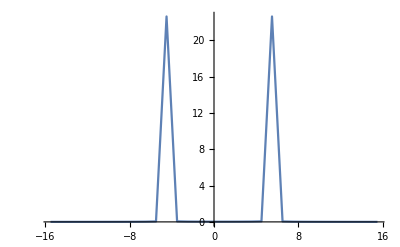

```mathematica
xy=Transpose[{Table[2*π*k/T,{k,-NN/2,NN/2}],Abs[fdf]}];
Select[xy,#[[1]]>-π*5&];
ListLinePlot[Select[Transpose[{Table[2*π*k/T,{k,-NN/2,NN/2}],Abs[fdf]}],#[[1]]>-π*5&&#[[1]]<π*5&],PlotRange->All]
```

```mathematica
(*Теорема Парсеваля (1/NN отсутвует, т.к. есть и там и там)*)
Total[Abs[fd]^2]-Total[Abs[fdf]^2]
```

4.80394×10^-13

```mathematica
(*к скорости сходимости*)
f[a_,b_]=a**b-b**a;
g[a_,b_]=a+b+1/2*f[a,b];
FullSimplify[g[a,g[b,a]]-2*a-b]
```

1/2 (-a**b+a**(a+b+1/2 (-a**b+b**a))+b**a-(a+b+1/2 (-a**b+b**a))**a)

```mathematica
(*4*)
```

```mathematica
Clear["Global`*"]
CalcWindow=10;(*ps*)
N0=127;

N0=N0+Boole[EvenQ[N0]];
Sech2Imp[T0_]:=Table[(*(-β2/γ/T0^2)^(1/2)*)N[Sech[t/T0]],{t,- CalcWindow, CalcWindow,2CalcWindow/(N0-1)}];
GaussImp[T0_]:=Table[(*(-β2/γ/T0^2)^(1/2)**)Exp[-(t/T0)^2],{t,- CalcWindow, CalcWindow,2CalcWindow/(N0-1)}];

β2=-22 ;γ=1.25 0 ;
Imp=Fourier[ Sech2Imp[0.08]]Exp[-I*Arg[Fourier[Sech2Imp[0.5]]]];
SpectrImp0=Imp;

D2Fourier=Table[-(Pi k/CalcWindow)^2,{k,0,N0/2}]~Join~Table[-(Pi (k-N0)/CalcWindow)^2,{k,Ceiling[N0/2],N0-1}];
FourierOp:=Exp[-I β2/2 D2Fourier h];
SpatialOp[x_List]:=Exp[I γ Abs[x]^2 h];

h=0.2/1000;

αdB=0.2;(*дБ/км; 20 - в 100 раз больше чем обычно*)
αpl=1(*Log[10]*αdB/10*);(*1/км*)
LossesOp:=Exp[-αpl*h/2];
c=3*10^-7;(*км/пс*)
λ0=1064*10^-9*10^-3;
ω0=2*π*c/λ0;
L=50h;

Imp=Sqrt[FourierOp*LossesOp]Imp;
Monitor[
For[ξ=h/2,ξ<L,ξ+=h,

Imp=InverseFourier[Imp];
Imp=Imp SpatialOp[Imp];
Imp=Imp LossesOp;
Imp=Fourier[Imp];
Imp=FourierOp Imp

],{ξ}]
```

```mathematica
Manipulate[{
Imp1=Imp*Exp[imβ2/2 D2Fourier 10*h ];
Imp1=InverseFourier[Imp1/Sqrt[FourierOp*LossesOp]];
SpectrImp=Fourier[Imp1];
temp=SpectrImp;
SpectrImp=RotateLeft[SpectrImp,(N0+1)/2];
λ=N[2*π*c/(Table[ω0,Dimensions[SpectrImp][[1]]]+Table[2*π*k/(2*CalcWindow),{k,-(N0-1)/2,(N0-1)/2}])*10^12];
ListPlot[Transpose[{λ,10*Log10[Abs[SpectrImp]^2]}],PlotRange->Automatic,ImageSize->Large],
sp=Interpolation[Transpose[{λ,10*Log10[Abs[SpectrImp]^2]}],InterpolationOrder->3];
Plot[sp[q]-Max[10*Log10[Abs[SpectrImp]^2]]+3,{q,1062,1066},ImageSize->Large],
dλ=(q/.FindRoot[sp[q]-Max[10*Log10[Abs[SpectrImp]^2]]+3,{q,1065}])-(a/.FindRoot[sp[a]-Max[10*Log10[Abs[SpectrImp]^2]]+3,{a,1063}])


}
,{{imβ2,0.1},0,100}]
```

```mathematica
Imp0=InverseFourier[Imp/Sqrt[FourierOp]];
SpectrImp0=Fourier[Imp0];
SpectrImp0=RotateLeft[SpectrImp0,(N0+1)/2];
```

0.99005

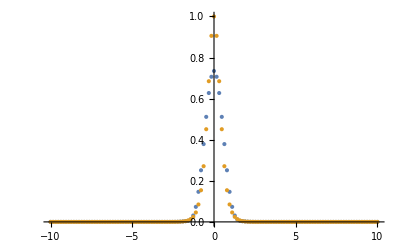

```mathematica
Exp[-αpl*L]
ListPlot[{RotateLeft[Abs[Imp0]^2,(N0+1)/2],Abs[Sech2Imp[0.5]]^2},PlotRange->All,DataRange->{-CalcWindow,CalcWindow}]
ListPlot[Arg[Imp0]];

ϕmax=π;
Textra=0;
SpectrImp=Imp0;
Specfin={Arg[SpectrImp[[1]]],Arg[SpectrImp[[2]]]};
For[i=3,i<=Length[SpectrImp],i+=1,
diff=Specfin[[i-1]]-Specfin[[i-2]];
If[(diff>=0&&Arg[SpectrImp[[i]]]-Arg[SpectrImp[[i-1]]]<-ϕmax),
Textra++];
If[(diff<0&&Arg[SpectrImp[[i]]]-Arg[SpectrImp[[i-1]]]>ϕmax),
Textra--];
AppendTo[Specfin, Arg[SpectrImp[[i]]]+Textra*2*π];
];
ListPlot[Specfin,PlotRange->All];

dω=ListCorrelate[{-1/2,0,1/2},Specfin];
dω=Insert[dω,2*(Specfin[[-1]]-Specfin[[-2]]),-1];
dω=-dω/(2*CalcWindow/(N0-1));
ListPlot[dω,PlotRange->All];

λ=N[2*π*c/(Table[ω0,Dimensions[SpectrImp0][[1]]]+Table[2*π*k/(2*CalcWindow),{k,-(N0-1)/2,(N0-1)/2}])*10^12];

ListPlot[Transpose[{λ,10Log[Abs[SpectrImp0]^2]}],PlotRange->Automatic,PlotRange->All];

ListPlot[Transpose[{λ,Arg[SpectrImp0]}]];
ListPlot[Arg[SpectrImp0]];
(*λcur=2*π*c/(ω0+dωcur)*10^12;(*нм*)
dλ=2*π*c/ω0/ω0*dωcur*10^12;*)
```

```mathematica
(*SpectrImp=RotateLeft[SpectrImp,(N0-1)/2];*)
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of RotateLeft[SpectrImp,1023].

```mathematica
(*Clear[ϕmax,Specfin]
ϕmax=π;
Manipulate[{
SpectrImp=Exp[-I β2/2 D2Fourier z];
Textra=0;
Specfin={Arg[SpectrImp[[1]]],Arg[SpectrImp[[2]]]};
For[i=3,i<=Length[SpectrImp],i+=1,
diff=Specfin[[i-1]]-Specfin[[i-2]];
If[(diff>=0&&Arg[SpectrImp[[i]]]-Arg[SpectrImp[[i-1]]]<-ϕmax),
Textra++];
If[(diff<0&&Arg[SpectrImp[[i]]]-Arg[SpectrImp[[i-1]]]>ϕmax),
Textra--];
AppendTo[Specfin, Arg[SpectrImp[[i]]]+Textra*2*π];
];
Specfin=RotateLeft[Specfin,(N0-1)/2];
ListPlot[Specfin,ImageSize->Large]},
{{z,0},0,L}
];*)
```

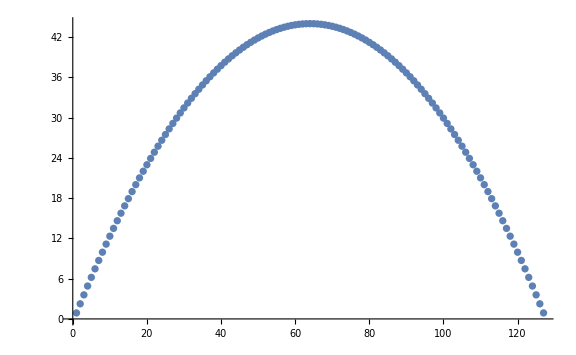

```mathematica
Textra=0;
ListPlot[Arg[Fourier[Sech2Imp[0.5]]*Exp[-I*Arg[Fourier[Sech2Imp[0.5]]]]]];
Specfin={Arg[SpectrImp[[1]]],Arg[SpectrImp[[2]]]};
For[i=3,i<=Length[SpectrImp],i+=1,
diff=Specfin[[i-1]]-Specfin[[i-2]];
If[(diff>=0&&Arg[SpectrImp[[i]]]-Arg[SpectrImp[[i-1]]]<-ϕmax),
Textra++];
If[(diff<0&&Arg[SpectrImp[[i]]]-Arg[SpectrImp[[i-1]]]>ϕmax),
Textra--];
AppendTo[Specfin, Arg[SpectrImp[[i]]]+Textra*2*π];
];
(*Specfin=RotateLeft[Specfin,(N0-1)/2];*)
ListPlot[Specfin,ImageSize->Large,PlotRange->All]
```

```mathematica
(*5*)
```

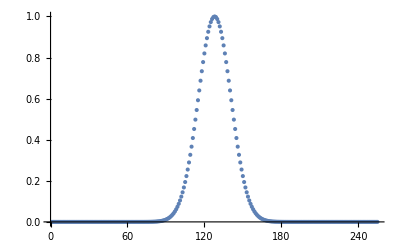

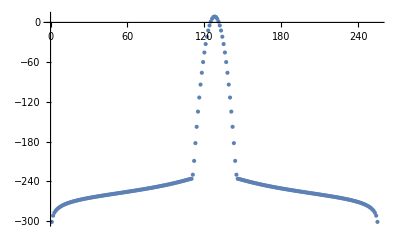

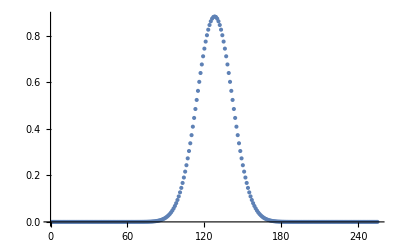

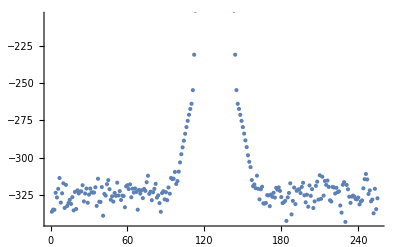

```mathematica
Clear["Global`*"]
CalcWindow=5;(*ps*)
N0=255;
L=0.006;

N0=N0+Boole[EvenQ[N0]];
β2=-22;
x=-0.05; (*дисперсия в пс^2*)

GaussImp[T0_]:=Table[Exp[-(t/T0)^2],{t,- CalcWindow, CalcWindow,2CalcWindow/(N0-1)}];
D2Fourier=Table[-(Pi k/CalcWindow)^2,{k,0,N0/2}]~Join~Table[-(Pi (k-N0)/CalcWindow)^2,{k,Ceiling[N0/2],N0-1}];

ListPlot[Abs[GaussImp[1]]^2,PlotRange->All]
Imp=Fourier[GaussImp[1]];
ListPlot[RotateLeft[10*Log10[Abs[Imp]^2],(N0+1)/2],PlotRange->All]

Imp=Imp*Exp[-I β2/2 D2Fourier L ];
Imp=Imp*Exp[-x/2 D2Fourier];
Imp=InverseFourier[Imp];

ListPlot[Abs[Imp]^2,PlotRange->All]
ListPlot[RotateLeft[10*Log10[Abs[Fourier[Imp]]^2],(N0+1)/2]]
```

```mathematica
x
```

```mathematica
(*6*)
```

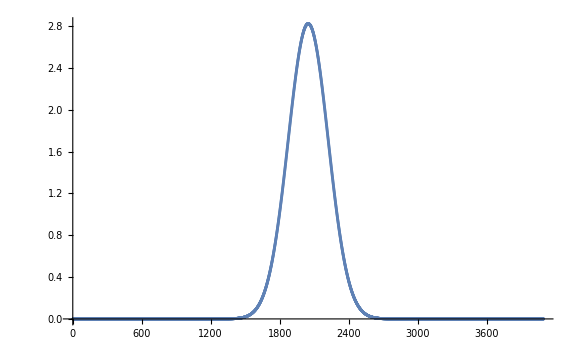

```mathematica
Clear["Global`*"]
CalcWindow=10;(*ps*)
N0=4095;
Tfwhm=1;
T0=Tfwhm/Sqrt[2*Log[2]];
E0=12.;(*пДж*)

c=3*10^-7;(*км/пс*)
λ0=1064*10^-9*10^-3;
ω0=2*π*c/λ0;
N0=N0+Boole[EvenQ[N0]];

P0=E0/Integrate[(Exp[-(t/T0)^2/2])^2,{t,-∞,∞}];
G6[t_]=√P0*Exp[-(t/T0)^2/2];
GaussImp6=Table[G6[t],{t,- CalcWindow, CalcWindow,2CalcWindow/(N0-1)}];
ListPlot[Abs[GaussImp6],PlotRange->All,ImageSize->Large]
```

```mathematica
β2=25;γ=5.8;h=0.0000001;
Imp=Fourier[GaussImp6];

D2Fourier=Table[-(Pi k/CalcWindow)^2,{k,0,N0/2}]~Join~Table[-(Pi (k-N0)/CalcWindow)^2,{k,Ceiling[N0/2],N0-1}];
FourierOp:=Exp[-I β2/2 D2Fourier h];
SpatialOp[x_List]:=Exp[I γ Abs[x]^2 h];

αdB=0.2;(*дБ/км; 20 - в 100 раз больше чем обычно*)
αpl=-1900;(*1/км*)
LossesOp:=Exp[-αpl*h/2];
L=0.006;
LD=1^2/β2;

Imp=Sqrt[FourierOp]Imp;
Monitor[
For[ξ=h/2,ξ<L,ξ+=h,

Imp=InverseFourier[Imp];
ImpCur=Imp;
Imp=Imp SpatialOp[Imp];
Imp=Imp LossesOp;

LNL=1/γ/Abs[Imp[[(N0+1)/2]]]^2;

Imp=Fourier[Imp];
Imp=FourierOp Imp;

h=Min[LNL/100,LD/10,10^-6];
],{ξ,ListPlot[Abs[ImpCur]^2,PlotRange->All,ImageSize->Large]}]
Imp=InverseFourier[Imp/Sqrt[FourierOp]];
SpectrImp=Fourier[Imp];
```

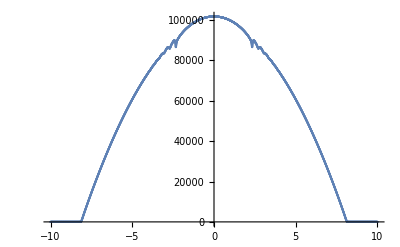

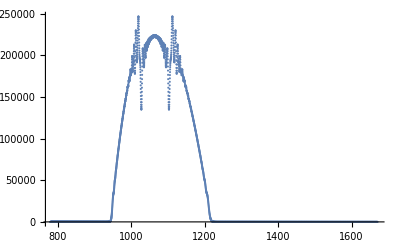

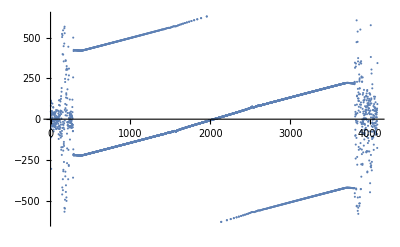

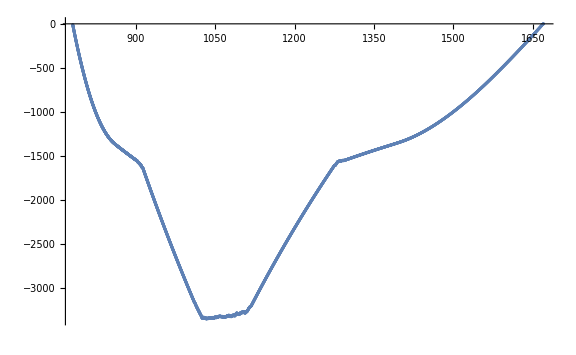

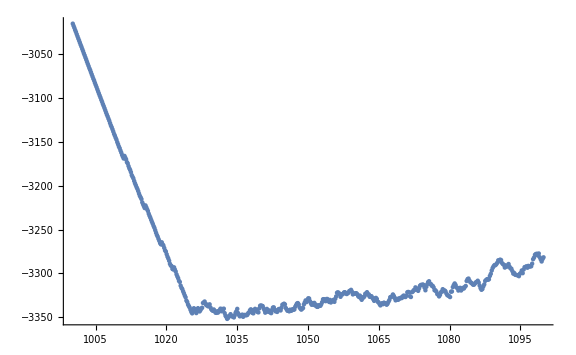

```mathematica
ListPlot[Abs[Imp]^2,PlotRange->All,DataRange->{-CalcWindow,CalcWindow}]
λ=N[2*π*c/(Table[ω0,Dimensions[SpectrImp][[1]]]+Table[2*π*k/(2*CalcWindow),{k,-(N0-1)/2,(N0-1)/2}])*10^12];
ListPlot[Transpose[{λ,RotateLeft[Abs[SpectrImp]^2,(N0+1)/2]}],PlotRange->Automatic]

dω=ListCorrelate[{-1/2,0,1/2},Arg[Imp]];
dω=Insert[dω,2*(Arg[Imp][[-1]]-Arg[Imp][[-2]]),-1];
dω=-dω/(2*CalcWindow/(N0-1));
ListPlot[dω]

Textra=0;ϕmax=π;
Specfin={Arg[SpectrImp[[1]]],Arg[SpectrImp[[2]]]};
For[i=3,i<=Length[SpectrImp],i+=1,
diff=Specfin[[i-1]]-Specfin[[i-2]];
If[(diff>=0&&Arg[SpectrImp[[i]]]-Arg[SpectrImp[[i-1]]]<-ϕmax),
Textra++];
If[(diff<0&&Arg[SpectrImp[[i]]]-Arg[SpectrImp[[i-1]]]>ϕmax),
Textra--];
AppendTo[Specfin, Arg[SpectrImp[[i]]]+Textra*2*π];
];
ListPlot[Transpose[{λ,Specfin}],PlotRange->All,ImageSize->Large]
ListPlot[Select[Transpose[{λ,Specfin}],#[[1]]>1000&&#[[1]]<1100&],ImageSize->Large]
```

```mathematica
(*Аналитический симиляритон*)
```

```mathematica
CalcWindow=10*(10^-12);(*s*)
E0=12.*(10^-12);(*Дж*)
β2=25*(10^-12)^2;γ=5.8;h=0.0000001;

g=1900;(*1/km*)
ϕ0=0;
Uin=E0;
A0=1/2*((g*Uin)/(√(γ*β2/2)))^(1/3);
Tp[z_]:=(6 √(γ*β2/2))/g*A0*Exp[g/3*z];
Φ[z_,T_]:=ϕ0+(3*γ*A0^2)/(2*g)*Exp[2/3*g*z]-g/(6*β2)*T^2;
A[z_,T_]:=A0*Exp[g/3*z]*√(1-(T/Tp[z])^2);
(*Aw[z_,T_]:=Aw0/(√z)*Exp[g/2 z]*Exp[-Λ*Abs[T]/z];
Φw[z_,T_]:=ϕw0+(β2*Λ^2)/(2*z)-T^2/(2*β2*z);*)

ψ[z_,T_]=Piecewise[{{A[z,T]*Exp[ⅈ*Φ[z,T]],Abs[T]<Tp[z]},{Aw[z,T]*Exp[ⅈ*Φw[z,T]],Abs[T]>=Tp[z]}}];

Manipulate[Show[Plot[Abs[ψ[z,t]]^2,{t,-Tp[z],Tp[z]},PlotRange->All,PlotStyle->Red],ListPlot[Abs[Imp]^2,PlotRange->All,DataRange->{-CalcWindow,CalcWindow}]],{{z,0.006},0,0.01}];
```